Question 1 : Find the first three roots of the Bessel Function

```mathematica
f[x_] = BesselJ[1,x]
root1 = FindRoot[f[x]==0,{x,0.}]
root2 = FindRoot[f[x]==0,{x,3.}]
root3 = FindRoot[f[x]==0,{x,6.}]
f[x]/.root1
f[x]/.root2
f[x]/.root3
```

BesselJ[1,x]

{x→0.}

{x→3.83171}

{x→7.01559}

0.

3.10014×10^-16

4.33604×10^-16

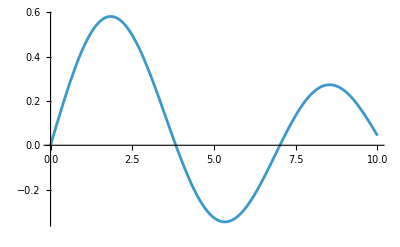

```mathematica
Plot[BesselJ[1,x],{x,0,10}]
```

The solutions seems to be sensible

Question 2 : Integrate the expression f(x) = sin(x) e^-x, and then take its derivative.

```mathematica
Clear[f]
f[x_] = Sin[x]Exp[-x]
integral [x_]= Integrate[f[x],x]
derivative[x_] = Simplify[ D[f[x],x] ]
```

ⅇ^-x Sin[x]

```mathematica
-1/2 ⅇ^-x (Cos[x]+Sin[x])
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
Simplify[D[integral[x],x]]
Integrate[derivative[x],x]
```

ⅇ^-x Sin[x]

ⅇ^-x Sin[x]

Question 3 : Solve the equation  x ln(x) - 3 x + 10 = 6, both symbolically and numerically.

```mathematica
Clear[f]
f[x_]= x Log[x] - 3 x + 10 
roots= Solve[f[x]==6,x]
N[roots]
N[f[x]/.roots[[1]]]
N[f[x]/.roots[[2]]]
```

10-3 x+x Log[x]

{{x→-4/ProductLog[-4/ⅇ^3]},{x→-4/ProductLog[-1,-4/ⅇ^3]}}

{{x→15.5229},{x→1.56883}}

6.

6.

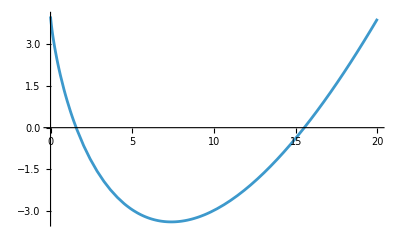

```mathematica
Plot[f[x]-6,{x,0,20}]
```

Seems also correct